# The Quest of the outlier

```mathematica
labeledYes = Table[reducedOxyYes80[[i,1]]-> ToString@i,{i,30}];
labeledNo = Table[reducedOxyNo80[[i,1]]->ToString@i,{i,30}];
```

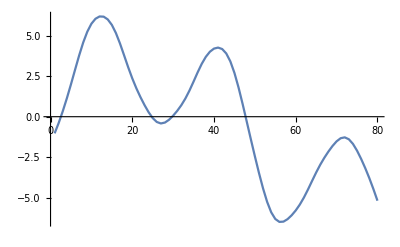

```mathematica
ListLinePlot[labeledNo[[1]],PlotLegends->Automatic]
```

```mathematica
labeledClusterYes = FindClusters[labeledYes,Method->"MeanShift"]//Column
```

{1,3,4,6,8,9,10,11,12,16,19,20,22,24,26,28,29}
{2,5,14,27}
{7,30}
{13,25}
{15,17,18,21,23}

```mathematica
check = FindClusters[reducedOxyYes80[[All,1]],Method->"MeanShift"];
```

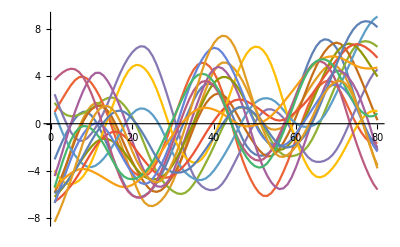
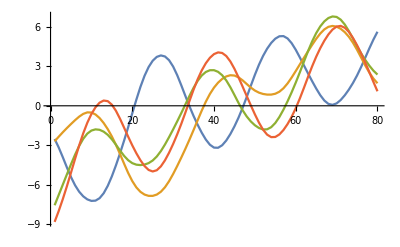
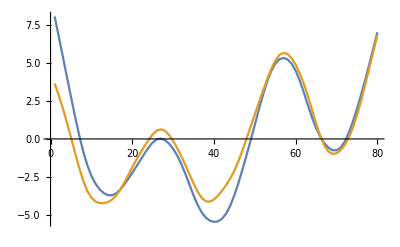
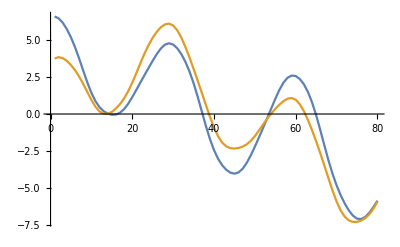
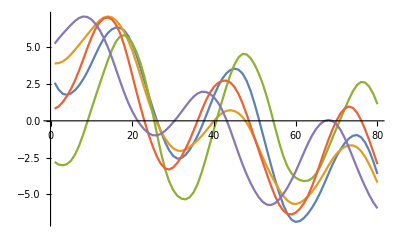

```mathematica
ListLinePlot/@check
```

```mathematica
labeledClusterNo = FindClusters[labeledNo,Method->"MeanShift"]//Column
```

{1,2,4,5,11,13,14,15,16,17,19,20,21,23,24,27,30}
{3,7,9,12,22,29}
{6,8,10,18,25,26,28}

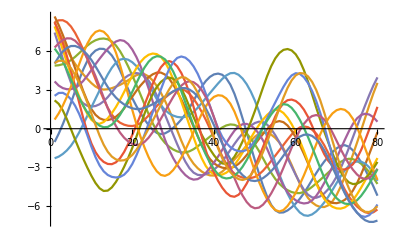
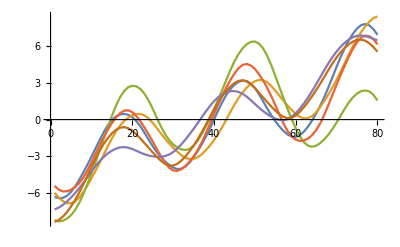
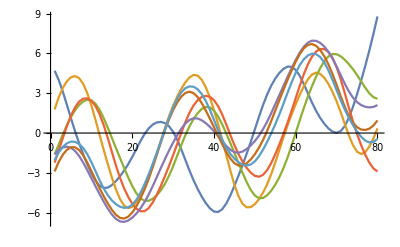

```mathematica
ListLinePlot/@FindClusters[reducedOxyNo80[[All,1]],Method->"MeanShift"]
```